```mathematica
Gam[x_,y_]:=-Series[1-I+I*(-Cos[x]-Cos[y]+(1/4)Cos[2y]),{x,0,6},{y,0,8}]
```

```mathematica
Gam[x,y]//ExpandAll
```

(-(1-(11 ⅈ)/4)-(ⅈ y^4)/8+(ⅈ y^6)/48-(ⅈ y^8)/640+O[y]^9)-(ⅈ x^2)/2+(ⅈ x^4)/24-(ⅈ x^6)/720+O[x]^7

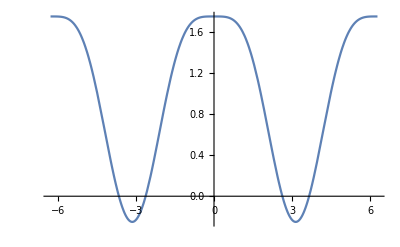

```mathematica
Plot[1+Cos[y]-(1/4)Cos[2y],{y,-2Pi,2Pi}]
```

Note that PhiHat[x,y] must look something like 1 + iP([x,y]) where P is positive homogeneous.

```mathematica
Plot3D[Abs[1+I*(-1-Cos[x]-Cos[y]+(1/4)Cos[2y])],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Cos[x]->(1/2)(E^(I*x)+E^(-I*x)),
Cos[2x]->(1/2)(E^(2I*x)+E^(-2I*x)),
Cos[y]->(1/2)(E^(I*y)+E^(-I*y)),
Cos[2y]->(1/2)(E^(2I*y)+E^(-2I*y))};
```

```mathematica
PhiHat[x_,y_]:=(1-I+I*(-Cos[x]-Cos[y]+(1/4)Cos[2y]))/((√137)/4)
```

Note that we must normalize by a real number so as not to introduce “real impurities”

```mathematica
Abs[PhiHat[0,0]]
```

1

```mathematica
PhiHat[x,y]/.RulePhi//ExpandAll
```

(4-4 ⅈ)/(√137)-(2 ⅈ ⅇ^(-ⅈ x))/(√137)-(2 ⅈ ⅇ^(ⅈ x))/(√137)-(2 ⅈ ⅇ^(-ⅈ y))/(√137)-(2 ⅈ ⅇ^(ⅈ y))/(√137)+(ⅈ ⅇ^(-2 ⅈ y))/(2 √137)+(ⅈ ⅇ^(2 ⅈ y))/(2 √137)